```mathematica
genericde={dself->Idself (1-m)/n,din->(1-m)(1/(n-1)-Idself 1/(n(n-1))),dout->m/(n d-n),(*
*)eself->Ieself (1-g)/n,ein->(1-g)(1/(n-1)-Ieself 1/(n(n-1))),eout->g/(n d-n)};
```

```mathematica
mychange=genericde/.Idself->1/.Ieself->0/.g->0
```

{dself→(1-m)/n,din→(1-m) (1/(-1+n)-1/((-1+n) n)),dout→m/(-n+d n),eself→0,ein→1/(-1+n),eout→0}

## BD

```mathematica
βBD/.mychange//FullSimplify
```

((-1+p) p ((-1+Qin-n Qin+n Qout) μ-d (-1+Qin+m (1+(-1+n) Qin-n Qout)+n (-Qin+Qout) μ)))/(d n μ)

```mathematica
βBDD/.mychange//FullSimplify
```

Qin-Qin μ

```mathematica
βBDI/.mychange//FullSimplify
```

(-d (-1+m) (1+(-1+n) Qin)+d m n Qout+(-1+Qin-n Qin+n (Qout-d Qout)) μ)/(d n)

```mathematica
tmp=(1-m)((n-1) Qin+1)/n+m  Qout-μ((n-1) Qin+n (d-1)Qout+1)/(n d) ;
tmp-βBDI/.mychange//FullSimplify
```

0

```mathematica
factorBD
```

((1-p) p)/μ

```mathematica
factorBD(βBDD-βBDI)-βBD//FullSimplify
```

0

```mathematica
tmp=βBD/.{Qin->QinM,Qout->QoutM}/.mychange//FullSimplify
```

-((-1+p) p (μ+d^2 (-1+m) (-2+μ) μ+d (m+(-3+μ) μ)))/(d (-(-1+d) μ (1+(-1+n) μ)+m (-1+μ) (1+d (-1+n) μ)))

```mathematica
Limit[tmp,d->∞]//FullSimplify
Limit[%,μ->0]//FullSimplify
```

-((-1+m) (-1+p) p (-2+μ))/(-1+m (-1+n) (-1+μ)+μ-n μ)

-(2 (-1+m) (-1+p) p)/(1+m (-1+n))

```mathematica
tmp=γBD/.{Qin->QinM,Qout->QoutM}/.mychange//FullSimplify
```

((-1+p) p (d m (-1+d n)+(-1+d (3-n+d (-2-2 m (-1+n)+n))) μ+d (1+d (-1+m)) (-1+n) μ^2))/(d (-(-1+d) μ (1+(-1+n) μ)+m (-1+μ) (1+d (-1+n) μ)))

```mathematica
Limit[tmp,μ->0]//FullSimplify
Limit[%,d->∞]//FullSimplify

Limit[tmp,d->∞]//FullSimplify
Limit[%,μ->0]//FullSimplify
```

-(-1+d n) (-1+p) p

n (-1+p) p (-∞)

((-1+p) p (m n+(-2-2 m (-1+n)+n) μ+(-1+m) (-1+n) μ^2))/(μ (-1+m (-1+n) (-1+μ)+μ-n μ))

(-1+p) p DirectedInfinity[Sign[m n]/Sign[-1+m-m n]]

```mathematica
γBD-factorBD(γBDD-γBDI)//FullSimplify
```

0

```mathematica
Normal[Series[tmp,{μ,0,1}]]
```

(1-d n) (-1+p) p+((1-2 d+d^2+d m-d^2 m+d n-2 d^2 n+d^3 n-d^3 m n+d^3 m n^2) (-1+p) p μ)/(d m)

```mathematica
γBDD
```

```mathematica
γBDI/.{Qin->QinM,Qout->QoutM}/.mychange//FullSimplify
Limit[factorBD*%,μ->0]
```

(-d m+d (1+d (-1+m)+m) μ+(-1+d-d m) μ^2)/(d (-(-1+d) μ (1+(-1+n) μ)+m (-1+μ) (1+d (-1+n) μ)))

((1-p) p DirectedInfinity[d])/d

```mathematica
tmp=γDB/.{Qin->QinM,Qout->QoutM}/.mychange//FullSimplify
Limit[tmp,μ->0]//FullSimplify
Limit[%,d->∞]//FullSimplify
```

((-1+p) p (-1+μ) (m (2+d (-1+m-n))+(1+d (-1+m)) (-1+n) μ))/(-(-1+d) μ (1+(-1+n) μ)+m (-1+μ) (1+d (-1+n) μ))

(2+d (-1+m-n)) (-1+p) p

(-1+m-n) (-1+p) p ∞

```mathematica
Limit[tmp,d->∞]//FullSimplify
Limit[%,μ->0]//FullSimplify
```

((-1+p) p (m n+(-2-2 m (-1+n)+n) μ+(-1+m) (-1+n) μ^2))/(μ (-1+m (-1+n) (-1+μ)+μ-n μ))

(-1+p) p DirectedInfinity[Sign[m n]/Sign[-1+m-m n]]

## DB

```mathematica
factorDB(βDBD-βDBI)-βDB//FullSimplify
```

-βDB+factorDB (βDBD-βDBI)

```mathematica
βDBD/.mychange//FullSimplify
```

βDBD

```mathematica
βDBI/.mychange//FullSimplify
```

βDBI

## Identity by descent

### Moran

#### In

```mathematica
qinm=QinM/.mychange//FullSimplify
```

-((-1+μ) (μ-d μ+m (-1+d μ)))/(-(-1+d) μ (1+(-1+n) μ)+m (-1+μ) (1+d (-1+n) μ))

```mathematica
qinms=((1-μ) (m+μ(d(1-m)-1)))/((d-1) μ (1+(n-1) μ)+m (1-μ) (1+d (n-1) μ));
```

```mathematica
qinms-qinm//FullSimplify
```

0

```mathematica
Collect[Denominator[qinms],μ,FullSimplify]
```

m+(-1+d-m+d m (-1+n)) μ+(-1+d-d m) (-1+n) μ^2

#### Out

```mathematica
qoutm=QoutM/.mychange//FullSimplify
```

(m (-1+μ))/(-(-1+d) μ (1+(-1+n) μ)+m (-1+μ) (1+d (-1+n) μ))

```mathematica
qoutms=(m (1-μ))/((d-1) μ (1+(n-1) μ)+m (1-μ) (1+d (n-1) μ));
```

```mathematica
qoutms-qoutm//FullSimplify
```

0

#### Plot

{d→4,n→4,μ→0.1}

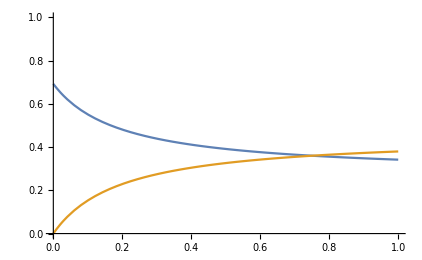

```mathematica
prs={d->4,n->4,μ->0.1}
Plot[{qinm/.prs,qoutm/.prs},{m,0,1},PlotRange->{0,1}]
```

{d→4,n→4,μ→0.1}

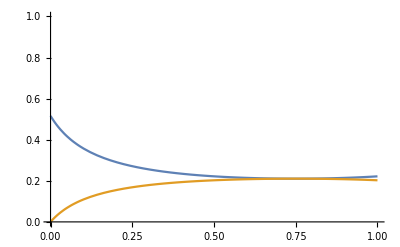

```mathematica
prs={d->4,n->4,μ->0.1}
Plot[{qinwfs/.prs,qoutwfs/.prs},{m,0,1},PlotRange->{0,1}]
```

```mathematica
LogLinearPlot[βBD/.{Qin->QinM,Qout->QoutM}/.mychange/.{n->4,μ->0.1,m->0.1,p->0.45},{d,4,10000000},PlotRange->All]
```

-Graphics-

### WF

#### In

```mathematica
qinwf=QinWF/.mychange//FullSimplify
```

(-d+(-1+d)/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)+1/(2 μ-μ^2))/(d (-1+n)+(-1+d)/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)+1/(2 μ-μ^2))

```mathematica
M1=(-1+d)/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2);
M2=1/(2 μ-μ^2);
```

```mathematica
qinwfs=(-d + M1+M2)/((n-1)d+M1+M2);
```

```mathematica
qinwf-qinwfs//FullSimplify
```

0

```mathematica
M1
```

(-1+d)/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)

```mathematica
M1s=(d-1)/(1-((d (1-m)-1)^2 (1-μ)^2)/(d-1)^2);
M1-M1s//FullSimplify
```

0

```mathematica
Limit[QinWF,μ->0]
Limit[qinwf,μ->0]
```

1

1

```mathematica
Limit[QinWF,d->∞]
Limit[qinwf,d->∞]//FullSimplify
```

((din^2-2 din dself+dself^2-(-1+m)^2) (-1+μ)^2)/(-1+2 m-m^2-2 m n+m^2 n+din^2 (-1+μ)^2-2 din dself (-1+μ)^2+dself^2 (-1+μ)^2+2 μ-4 m μ+2 m^2 μ-2 n μ+4 m n μ-2 m^2 n μ-μ^2+2 m μ^2-m^2 μ^2+n μ^2-2 m n μ^2+m^2 n μ^2)

-((-1+m)^2 (-1+μ)^2)/(-1-2 m (-1+n) (-1+μ)^2+m^2 (-1+n) (-1+μ)^2+(-1+n) (-2+μ) μ)

#### Out

```mathematica
qoutwf=QoutWF/.mychange//FullSimplify
```

(-1/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)+1/(2 μ-μ^2))/(d (-1+n)+(-1+d)/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)+1/(2 μ-μ^2))

```mathematica
qoutwfs=(-1/(d-1)M1+M2)/(d(n-1)+M1+M2)//FullSimplify
```

(-1/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)+1/(2 μ-μ^2))/(d (-1+n)+(-1+d)/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)+1/(2 μ-μ^2))

```mathematica
qoutwfs-qoutwf//FullSimplify
```

0

```mathematica
ExportForR[x_]:=Module[{xx},xx=x/.{μ->mu,d->ndemes};xx]
```

```mathematica
ExportForR[qinm]
```

-((-1+mu) (mu-mu ndemes+m (-1+mu ndemes)))/(-mu (1+mu (-1+n)) (-1+ndemes)+m (-1+mu) (1+mu (-1+n) ndemes))

#### Export to R

Rewrite the Greek letters

```mathematica
GreekTerms={ω->sel, μ->mut}
```

{ω→sel,μ→mut}

Common parts to all functions

```mathematica
FunctionPartB=" <- function(p, sel, mut, m, g, n, d, Idself, Ieself){
## Arguments:
#  p   mutation bias
#  sel intensity of selection
#  mut mutation probability
#  m   emigration probability
#  g   proportion of interactions out of the group (interaction equivalent of m)
#  n   deme size
#  d   number of demes
#  Idself whether reproduction in site where the parent is
#  Ieself whether interactions with oneself
return(
";
FunctionPartE=")
}";
```

Function to translate Mathematica to R

```mathematica
ToRForm[x_]:=ToString[x/.GreekTerms//CForm]
```

Do it for Q

```mathematica
RtxtQinM="QinM "<>FunctionPartB<>ToRForm[QinM/.genericde//FullSimplify]<>FunctionPartE;
RtxtQoutM="QoutM "<>FunctionPartB<>ToRForm[QoutM/.genericde//FullSimplify]<>FunctionPartE;
RtxtQinWF="QinWF "<>FunctionPartB<>ToRForm[QinWF/.genericde//FullSimplify]<>FunctionPartE;
RtxtQoutWF="QoutWF "<>FunctionPartB<>ToRForm[QoutWF/.genericde//FullSimplify]<>FunctionPartE;
```

Define Power function in R

```mathematica
PowerDef="Power <- function(a,b) return(a^b)";
```

Combine all texts

```mathematica
Rtxt=PowerDef<>"

"<>RtxtQinM<>"

"<>RtxtQoutM<>"

"<>RtxtQinWF<>"

"<>RtxtQoutWF;
```

Export to txt file (Mathematica did not want R)

```mathematica
Export["Documents/Work/Projects/2016_SocEvolSubdivPop/Programs/Mathematica/analyticsQ.txt",Rtxt]
```

Documents/Work/Projects/2016_SocEvolSubdivPop/Programs/Mathematica/analyticsQ.txt

Convert the file extension to R

```mathematica
<<"!mv Documents/Work/Projects/2016_SocEvolSubdivPop/Programs/Mathematica/analyticsQ.txt Documents/Work/Projects/2016_SocEvolSubdivPop/Programs/Mathematica/analyticsQ.R"
```

## Test

```mathematica
tmp=(-d+(-1+d)/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)+1/(2 μ-μ^2))/(d (-1+n)+(-1+d)/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)+1/(2 μ-μ^2))//Factor
FullSimplify[Numerator[tmp]]
FullSimplify[Denominator[tmp]]
```

-(((-1+μ)^2 (2 m-2 d m+d m^2-2 μ+4 d μ-2 d^2 μ-4 d m μ+4 d^2 m μ-2 d^2 m^2 μ+μ^2-2 d μ^2+d^2 μ^2+2 d m μ^2-2 d^2 m μ^2+d^2 m^2 μ^2))/(-2 m+2 d m-d m^2+2 μ-4 d μ+2 d^2 μ+4 m μ-4 d^2 m μ+2 d m^2 μ+2 d^2 m^2 μ-4 d m n μ+4 d^2 m n μ-2 d^2 m^2 n μ-5 μ^2+10 d μ^2-5 d^2 μ^2-2 m μ^2-8 d m μ^2+10 d^2 m μ^2-d m^2 μ^2-5 d^2 m^2 μ^2+4 n μ^2-8 d n μ^2+4 d^2 n μ^2+10 d m n μ^2-10 d^2 m n μ^2+5 d^2 m^2 n μ^2+4 μ^3-8 d μ^3+4 d^2 μ^3+8 d m μ^3-8 d^2 m μ^3+4 d^2 m^2 μ^3-4 n μ^3+8 d n μ^3-4 d^2 n μ^3-8 d m n μ^3+8 d^2 m n μ^3-4 d^2 m^2 n μ^3-μ^4+2 d μ^4-d^2 μ^4-2 d m μ^4+2 d^2 m μ^4-d^2 m^2 μ^4+n μ^4-2 d n μ^4+d^2 n μ^4+2 d m n μ^4-2 d^2 m n μ^4+d^2 m^2 n μ^4))

-(-1+μ)^2 ((2+d (-2+m)) m-2 (1+d (-1+m))^2 μ+(1+d (-1+m))^2 μ^2)

(-1+d)^2 (-2+μ) μ (-1+(-1+n) (-2+μ) μ)-2 (-1+d) m (-1+μ)^2 (-1+d (-1+n) (-2+μ) μ)+d m^2 (-1+μ)^2 (-1+d (-1+n) (-2+μ) μ)

```mathematica
FullSimplify[tmp/.μ->1-nμ]
```

-(nμ^2 (-(-1+d) (-1+d (-1+m)^2+2 m)+(1+d (-1+m))^2 nμ^2))/((-1+d) (-1+d (-1+m)^2+2 m) nμ^2-(1+d (-1+m))^2 nμ^4+n (-1+nμ^2) (-(-1+d)^2+(1+d (-1+m))^2 nμ^2))

```mathematica
QinM
```

((-1+μ) ((-1+d) (1+din-dself) μ+m (1+din-dself-(d+din-dself) μ)))/(m (-1+μ) (1+din-dself+(-din+dself+d (-1+n)) μ)+(-1+d) μ (-1+dself+din (-1+μ)+μ-(dself+n) μ))

```mathematica
Collect[tmp//FullSimplify,μ,FullSimplify]
```

-((-1+μ)^2 ((2+d (-2+m)) m-2 (1+d (-1+m))^2 μ+(1+d (-1+m))^2 μ^2))/((-1+d)^2 (-2+μ) μ (-1+(-1+n) (-2+μ) μ)-2 (-1+d) m (-1+μ)^2 (-1+d (-1+n) (-2+μ) μ)+d m^2 (-1+μ)^2 (-1+d (-1+n) (-2+μ) μ))

```mathematica
tmp//FullSimplify
```

-((-1+μ)^2 ((2+d (-2+m)) m-2 (1+d (-1+m))^2 μ+(1+d (-1+m))^2 μ^2))/((-1+d)^2 (-2+μ) μ (-1+(-1+n) (-2+μ) μ)-2 (-1+d) m (-1+μ)^2 (-1+d (-1+n) (-2+μ) μ)+d m^2 (-1+μ)^2 (-1+d (-1+n) (-2+μ) μ))

```mathematica
Collect[Numerator[tmp], μ,FullSimplify]
```

-(2+d (-2+m)) m+2 (1+2 m+d (-2+d (-1+m)^2+m^2)) μ+(-5-2 m-d (-10+5 d (-1+m)^2+m (8+m))) μ^2+4 (1+d (-1+m))^2 μ^3-(1+d (-1+m))^2 μ^4

### Derivatives

#### Moran

```mathematica
D[qinms,m]//FullSimplify
Solve[%==0]
```

((-1+d)^2 n (-1+μ) μ^2)/((-1+d) μ (1+(-1+n) μ)-m (-1+μ) (1+d (-1+n) μ))^2

{{d→1},{n→0},{μ→0},{μ→1}}

```mathematica
D[qoutms,m]//FullSimplify
Solve[%==0]
```

-((-1+d) (-1+μ) μ (1+(-1+n) μ))/((-1+d) μ (1+(-1+n) μ)-m (-1+μ) (1+d (-1+n) μ))^2

{{d→1},{n→(-1+μ)/μ},{μ→0},{μ→1}}

#### WF

```mathematica
qinwfs
```

(-d+(-1+d)/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)+1/(2 μ-μ^2))/(d (-1+n)+(-1+d)/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)+1/(2 μ-μ^2))

```mathematica
1/(1-(1-μ)^2)-M2//Simplify
```

0

```mathematica
sols=Solve[qinwfs==0]//FullSimplify
```

{{m→(-1+d-2 (-1+d) d μ+(-1+d) d μ^2-√((-1+d)^2 (1+d (-2+μ) μ)))/(d (1+d (-2+μ) μ))},{m→(-1+d-2 (-1+d) d μ+(-1+d) d μ^2+√((-1+d)^2 (1+d (-2+μ) μ)))/(d (1+d (-2+μ) μ))},{μ→1},{d→0,m→-1/2 (-2+μ) μ}}

```mathematica
sols/.{d->10,μ->0.001}
```

{{m→-0.00913265},{m→1.80913},{0.001→1},{10→0,m→0.0009995}}

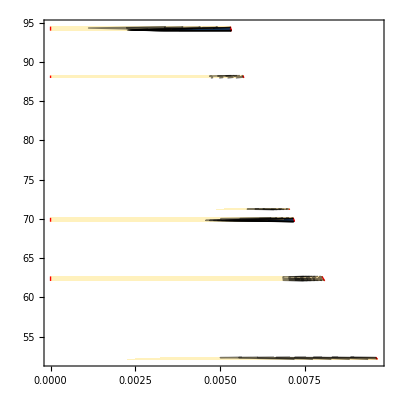

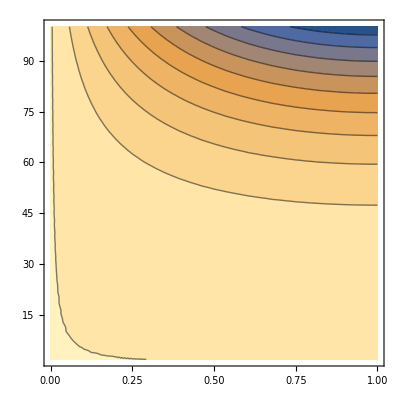

```mathematica
ContourPlot[(-1+d-2 (-1+d) d μ+(-1+d) d μ^2-√((-1+d)^2 (1+d (-2+μ) μ)))/(d (1+d (-2+μ) μ)),{μ,0,1},{d,2,100},PlotRange->All,RegionFunction->Function[{x,y,z},(-1+y)^2 (1+y (-2+x) x)>0],BoundaryStyle->Red]
ContourPlot[(-1+d)^2 (1+d (-2+μ) μ),{μ,0,1},{d,2,100},PlotRange->All]
```

```mathematica
qoutwfs
```

(-1/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)+1/(2 μ-μ^2))/(d (-1+n)+(-1+d)/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)+1/(2 μ-μ^2))

```mathematica
Solve[qoutwfs==0]
```

{{m→0},{m→(2 (-1+d))/d},{μ→1}}

```mathematica
M1-((d-1)/(1-((d (1-m)-1)^2 (1-μ)^2)/(d-1)^2))//FullSimplify
```

0

```mathematica
M1//Factor//FullSimplify
```

-(-1+d)^3/((-2+d (2+m (-1+μ)-μ)+μ) (-d m+μ+d (-1+m) μ))

```mathematica
D[qinwfs,m]//FullSimplify
Solve[%==0]
```

(2 (-1+d)^3 (1+d (-1+m)) n (-2+μ)^2 (-1+μ)^2 μ^2)/(((-1+d)^2 (-2+μ) μ (-1+(-1+n) (-2+μ) μ)-2 (-1+d) m (-1+μ)^2 (-1+d (-1+n) (-2+μ) μ)+d m^2 (-1+μ)^2 (-1+d (-1+n) (-2+μ) μ))^2)

{{d→1},{m→(-1+d)/d},{n→0},{μ→0},{μ→1},{μ→2}}

```mathematica
D[qoutwfs,m]//FullSimplify
Solve[%==0]
```

-(2 (-1+d)^2 (1+d (-1+m)) (-2+μ) (-1+μ)^2 μ (-1+(-1+n) (-2+μ) μ))/(((-1+d)^2 (-2+μ) μ (-1+(-1+n) (-2+μ) μ)-2 (-1+d) m (-1+μ)^2 (-1+d (-1+n) (-2+μ) μ)+d m^2 (-1+μ)^2 (-1+d (-1+n) (-2+μ) μ))^2)

{{d→1},{m→(-1+d)/d},{n→(-1+μ)^2/((-2+μ) μ)},{μ→0},{μ→1},{μ→2}}

```mathematica
Solve[(1+d (-1+m))==0,m]
```

{{m→(-1+d)/d}}

```mathematica
Limit[qoutwfs,μ->0]
Limit[qinwfs,μ->0]
```

1

1

```mathematica
Limit[qoutwfs,d->∞]
Limit[qinwfs,d->∞]//FullSimplify
Limit[%,μ->0]//FullSimplify
1/n+(n-1)/n%//FullSimplify
```

0

-((-1+m)^2 (-1+μ)^2)/(-1-2 m (-1+n) (-1+μ)^2+m^2 (-1+n) (-1+μ)^2+(-1+n) (-2+μ) μ)

-(-1+m)^2/(-1+(-2+m) m (-1+n))

-1/(-1+(-2+m) m (-1+n))

```mathematica
-(-1+m)^2/(-1+(-2+m) m (-1+n))-((1-m)^2/(1+(2-m) m (n-1)))//FullSimplify
```

0

```mathematica
Limit[qinms,d->∞]//FullSimplify
Limit[%,μ->0]//FullSimplify
1/n+(n-1)/n%//FullSimplify
```

(-1+m+μ-m μ)/(-1+m (-1+n) (-1+μ)+μ-n μ)

(-1+m)/(-1+m-m n)

1/(1+m (-1+n))

```mathematica
(-1+m)/(-1+m-m n)-((1-m)/(1+m (n-1)))//Simplify
```

0

#### Limits

```mathematica
BD=((-1+p) p ((-1+Qin-n Qin+n Qout) μ-d (-1+Qin+m (1+(-1+n) Qin-n Qout)+n (-Qin+Qout) μ)))/(d n μ)/.mychange/.{Qin->qinms,Qout->qoutms}//FullSimplify
```

-((-1+p) p (μ+d^2 (-1+m) (-2+μ) μ+d (m+(-3+μ) μ)))/(d (-(-1+d) μ (1+(-1+n) μ)+m (-1+μ) (1+d (-1+n) μ)))

```mathematica
Limit[BD,d->∞]//FullSimplify
Limit[%,μ->0]//FullSimplify
```

-((-1+m) (-1+p) p (-2+μ))/(-1+m (-1+n) (-1+μ)+μ-n μ)

-(2 (-1+m) (-1+p) p)/(1+m (-1+n))